# Volume and surface area of Roche lobes

Author : Martin Horvat, April 2016

## Theory

```mathematica
v1[x_,phi_]:=R[x,phi]^(1/2){0,Cos[phi],Sin[phi]}+{x,0,0}
```

```mathematica
dA1=Cross[D[v1[x,phi],x],D[v1[x,phi],phi]]
```

{1/2 Cos[phi]^2 R^(1,0)[x,phi]+1/2 Sin[phi]^2 R^(1,0)[x,phi],-Cos[phi] √R[x,phi]-(Sin[phi] R^(0,1)[x,phi])/(2 √R[x,phi]),-√R[x,phi] Sin[phi]+(Cos[phi] R^(0,1)[x,phi])/(2 √R[x,phi])}

```mathematica
Simplify[dA1.dA1]
```

1/4 (4 R[x,phi]+((R^(0,1)[x,phi])^2)/R[x,phi]+(R^(1,0)[x,phi])^2)

## Cylindric coordinate system

```mathematica
Omega[x_,y_,z_,{q_,F_,d_}]=FullSimplify[1/Sqrt[x^2+y^2+z^2]+q(1/Sqrt[x^2+y^2+z^2-2x d+d^2]-x/d^2)+1/2F^2(1+q)(x^2+y^2)]
```

-(q x)/d^2+1/2 F^2 (1+q) (x^2+y^2)+q/(√((d-x)^2+y^2+z^2))+1/(√(x^2+y^2+z^2))

```mathematica
CylOmega[R_,t_,c_,{q_,b_}]=FullSimplify[d Omega[d t,d R^(1/2) Cos[phi],d R^(1/2)*Sin[phi],{q,F,d}],d>0]/.d^3F^2->b/(1+q)/.Cos[phi]^2->c
```

1/2 ((2 q)/(√(R+(-1+t)^2))-2 q t+2/(√(R+t^2))+b (c R+t^2))

```mathematica
(* Derivative dR/dt, R = r^2 *)
```

```mathematica
Omegat[R_,t_,c_,{q_,b_}]=FullSimplify[D[CylOmega[R,t,c,{q,b}],t]]
OmegaR[R_,t_,c_,{q_,b_}]=FullSimplify[D[CylOmega[R,t,c,{q,b}],R]]
Omegac[R_,t_,c_,{q_,b_}]=FullSimplify[D[CylOmega[R,t,c,{q,b}],c]]
```

1/2 (-2 q-(2 q (-1+t))/((R+(-1+t)^2)^(3/2))+2 b t-(2 t)/((R+t^2)^(3/2)))

1/2 (b c-q/((R+(-1+t)^2)^(3/2))-1/((R+t^2)^(3/2)))

(b R)/2

```mathematica
DRDt[R_,t_,c_,{q_,b_}]=-Omegat[R,t,c,{q,b}]/OmegaR[R,t,c,{q,b}]
```

(2 q+(2 q (-1+t))/((R+(-1+t)^2)^(3/2))-2 b t+(2 t)/((R+t^2)^(3/2)))/(b c-q/((R+(-1+t)^2)^(3/2))-1/((R+t^2)^(3/2)))

```mathematica
DRDc[R_,t_,c_,{q_,b_}]=-Omegac[R,t,c,{q,b}]/OmegaR[R,t,c,{q,b}]
```

-(b R)/(b c-q/((R+(-1+t)^2)^(3/2))-1/((R+t^2)^(3/2)))

```mathematica
FullSimplify[DRDt[R,t,c,{q,b}]/.{1/(R+t^2)^(3/2)->f1,1/(R+(-1+t)^2)^(3/2)->f2}]
```

-(2 (q (1+f2 (-1+t))+(-b+f1) t))/(-b c+f1+f2 q)

```mathematica
FullSimplify[DRDc[R,t,c,{q,b}]/.{1/(R+t^2)^(3/2)->f1,1/(R+(-1+t)^2)^(3/2)->f2}]
```

-(b R)/(b c-f1-f2 q)

```mathematica
Clear[CylR];
CylR[x_?NumericQ,phi_?NumericQ,Omega0_?NumericQ,{q_,F_,delta_}]:=Module[{t,R,solR,a,b,c,sol},
t=x/delta;
a=delta^3F^2;
b=a(1+q);
c=Cos[phi]^2;
solR=Min[R/.NSolve[{CylOmega[R,t,c,{q,b}]==delta Omega0,R>0},R,Reals]];
delta^2solR
]

Clear[CylA];
CylA[x_?NumericQ,phi_?NumericQ,Omega0_?NumericQ,{q_,F_,delta_}]:=Module[{t,R,solR,a,b,c,sol},
t=x/delta;
a=delta^3F^2;
b=a(1+q);
c=Cos[phi]^2;
solR=Min[R/.NSolve[{CylOmega[R,t,c,{q,b}]==delta Omega0,R>0},R,Reals]];
delta Sqrt[solR+ DRDc[solR,t,c,{q,b}]^2c(1-c)/solR+DRDt[solR,t,c,{q,b}]^2/4]
]

Clear[CylS];
CylS[x_?NumericQ,phi_?NumericQ,Omega0_?NumericQ,{q_,F_,delta_}]:=Module[{t,R,solR,a,b,c,sol},
t=x/delta;
a=delta^3F^2;
b=a(1+q);
c=Cos[phi]^2;
solR=Min[R/.NSolve[{CylOmega[R,t,c,{q,b}]==delta Omega0,R>0},R,Reals]];
delta {solR, DRDt[solR,t,c,{q,b}],DRDc[solR,t,c,{q,b}]/solR,solR+ DRDc[solR,t,c,{q,b}]^2c(1-c)/solR+DRDt[solR,t,c,{q,b}]^2/4}
]
```

## Volume and surface -- overcontact case

```mathematica
par=SetPrecision[{0.5,0.5,1},30];
Omega0=SetPrecision[2.65,30];
s1=Sort[x/.Solve[Omega[x,0,0,par]==Omega0,x,Reals,WorkingPrecision->30]]
CForm/@s1
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{-2.2294038924731011210032146114,-0.49447358607935408230539738444,1.230551900314990501257141007,5.1037881515184548949306435149}

{-2.2294038924731011210032146114,-0.49447358607935408230539738444,1.23055190031499050125714100697,5.1037881515184548949306435149}

```mathematica
surf1=4NIntegrate[
CylA[x,phi,Omega0,par],
{x,s1[[2]],s1[[3]]},
{phi,0,Pi/2},WorkingPrecision->20]
```

3.7269717150611265036

```mathematica
vol1=2NIntegrate[
CylR[x,phi,Omega0,par],
{x,s1[[2]],s1[[3]]},
{phi,0,Pi/2}]
```

0.525896

```mathematica
2^16
```

65536

## Volume and surface -- generic detached case

```mathematica
par=SetPrecision[{2,1,1},30]; (*(q,F,d)*)
Omega0=SetPrecision[10,30];
s1=Sort[x/.Solve[Omega[x,0,0,par]==Omega0,x,Reals,WorkingPrecision->30]]
CForm/@s1
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{-1.8391249469955798334138880188,-0.1258156863540126334386200194,0.12594600792566138261477245729,0.78664043255994793825529888794,1.2128870650303101396317036886,3.1742232781240649694715208475}

{-1.83912494699557983341388801884,-0.125815686354012633438620019399,0.125946007925661382614772457291,0.78664043255994793825529888794,1.21288706503031013963170368856,3.17422327812406496947152084752}

```mathematica
surf1=4NIntegrate[
CylA[x,phi,Omega0,par],
{x,s1[[2]],s1[[3]]},
{phi,0,Pi/2}]
```

0.197133

```mathematica
vol1=2NIntegrate[
CylR[x,phi,Omega0,par],
{x,s1[[2]],s1[[3]]},
{phi,0,Pi/2}]
```

0.00823009

## Volume and surface -- extreme detached case

```mathematica
par=SetPrecision[{3.00348934885*10^-6,365,1},30];
Omega0=SetPrecision[30000,30];
s1=Sort[x/.Solve[Omega[x,0,0,par]==Omega0,x,Reals,WorkingPrecision->30]]
CForm/@s1
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{-0.6710754050761449818394233515,-0.000033333333418908445687502868699,0.0000333333334189084456875031159,0.67107540503920215760126239212}

{-0.6710754050761449818394233515,-0.000033333333418908445687502868699,0.0000333333334189084456875031159,0.67107540503920215760126239212}

```mathematica
surf1=4NIntegrate[
CylA[x,phi,Omega0,par],
{x,s1[[2]],s1[[3]]},
{phi,0,Pi/2},WorkingPrecision->20]
```

1.3962634063282837442×10^-8

```mathematica
vol1=2NIntegrate[
CylR[x,phi,Omega0,par],
{x,s1[[2]],s1[[3]]},
{phi,0,Pi/2},WorkingPrecision->20]
```

1.5514037872055681352×10^-13

## Volume and surface, detached case -- analytical approximation, omega -> infty

```mathematica
(* λ= Sin[theta]Cos[phi], mu=Sin[theta]Sin[phi], u=1-nu^2, nu=Cos[theta], W = d Omega *)
```

```mathematica
W=1/ρ+ q(1/Sqrt[1-2 ρ λ+ρ^2]-λ ρ)+1/2 b ρ^2 u
```

1/ρ+1/2 b u ρ^2+q (-λ ρ+1/(√(1-2 λ ρ+ρ^2)))

```mathematica
n=10;
m=10;
(* s = 1/W *)
Rho[λ_,u_,{s_,b_,q_}]=Simplify[InverseSeries[Series[1/W,{ρ,0,n}],s]];
```

```mathematica
V[s_,b_,q_]=2/3 Integrate[Normal[Series[Rho[Sin[theta]Cos[phi],Sin[theta]^2,{s,b,q}]^3 Sin[theta]/s^3,{s,0,m}]]*s^3,{theta,0,Pi/2},{phi,0,2Pi}]
```

4/105 π s^3 (35+35 b s^3+56 b^2 s^6+1260 q^7 s^7+1575 q^8 s^8+110 b^3 s^9+1925 q^9 s^9+490 q^6 s^6 (2+33 b s^3)+105 q^5 s^5 (7+84 b s^3+132 s^4)+105 q^4 s^4 (5+42 b s^3+36 s^4+44 b s^5)+q^3 s^3 (350+756 s^4+935 s^6+9240 b^2 s^6+140 b s^3 (14+9 s^2))+q s (105+14 b s^3 (15+2 s^2)+2 b^2 s^6 (252+55 s^2))+q^2 s^2 (210+84 s^4+75 s^6+2520 b^2 s^6+b s^3 (735+252 s^2+440 s^4)))

```mathematica
Collect[V[s,b,q]/(4 Pi/3 s^3),s,Simplify]
```

1+3 q s+6 q^2 s^2+(b+10 q^3) s^3+(6 b q+15 q^4) s^4+21 q^2 (b+q^3) s^5+4/5 (2 b^2+b q+3 q^2+70 b q^3+35 q^6) s^6+18/5 q (4 b^2+2 b q+6 q^2+35 b q^3+10 q^6) s^7+3/7 q^2 (5+168 b^2+252 q^2+105 q^6+84 b (q+7 q^3)) s^8+11/7 (2 b^3+2 b^2 (q+84 q^3)+q^3 (17+252 q^2+35 q^6)+b (8 q^2+84 q^4+294 q^6)) s^9

```mathematica
Simplify[V[s,0,0]]
```

(4 π s^3)/3

```mathematica
Vc=FullSimplify[CoefficientList[V[s,b,q]*(3/(4 Pi)),s]]
```

{0,0,0,1,3 q,6 q^2,b+10 q^3,6 b q+15 q^4,21 q^2 (b+q^3),4/5 (2 b^2+b q+3 q^2+70 b q^3+35 q^6),18/5 q (4 b^2+2 b q+6 q^2+35 b q^3+10 q^6),3/7 q^2 (5+21 (8 b^2+4 b (q+7 q^3)+q^2 (12+5 q^4))),11/7 (2 b^3+2 b^2 (q+84 q^3)+q^3 (17+252 q^2+35 q^6)+b (8 q^2+84 q^4+294 q^6))}

```mathematica
Drop[Vc,3]
```

{1,3 q,6 q^2,b+10 q^3,6 b q+15 q^4,21 q^2 (b+q^3),4/5 (2 b^2+b q+3 q^2+70 b q^3+35 q^6),18/5 q (4 b^2+2 b q+6 q^2+35 b q^3+10 q^6),3/7 q^2 (5+21 (8 b^2+4 b (q+7 q^3)+q^2 (12+5 q^4))),11/7 (2 b^3+2 b^2 (q+84 q^3)+q^3 (17+252 q^2+35 q^6)+b (8 q^2+84 q^4+294 q^6))}

```mathematica
Vcc=HornerForm[#,q]&/@Drop[Vc,3]
```

{1,3 q,6 q^2,b+10 q^3,q (6 b+15 q^3),q^2 (21 b+21 q^3),(8 b^2)/5+q ((4 b)/5+q (12/5+q (56 b+28 q^3))),q ((72 b^2)/5+q ((36 b)/5+q (108/5+q (126 b+36 q^3)))),q^2 (15/7+72 b^2+q (36 b+q (108+q (252 b+45 q^3)))),(22 b^3)/7+q ((22 b^2)/7+q ((88 b)/7+q (187/7+264 b^2+q (132 b+q (396+q (462 b+55 q^3))))))}

```mathematica
CForm/@Vcc
```

{1,3*q,6*Power(q,2),b + 10*Power(q,3),q*(6*b + 15*Power(q,3)),Power(q,2)*(21*b + 21*Power(q,3)),(8*Power(b,2))/5. + q*((4*b)/5. + q*(2.4 + q*(56*b + 28*Power(q,3)))),q*((72*Power(b,2))/5. + q*((36*b)/5. + q*(21.6 + q*(126*b + 36*Power(q,3))))),Power(q,2)*(2.142857142857143 + 72*Power(b,2) + q*(36*b + q*(108 + q*(252*b + 45*Power(q,3))))),(22*Power(b,3))/7. + q*((22*Power(b,2))/7. + q*((88*b)/7. + q*(26.714285714285715 + 264*Power(b,2) + q*(132*b + q*(396 + q*(462*b + 55*Power(q,3)))))))}

```mathematica
A[s_,b_,q_]=
Module[{R,S,theta,phi},
R=Rho[Sin[theta]Cos[phi],Sin[theta]^2,{s,b,q}];
S=Normal[Series[R Sqrt[(R^2+D[R,theta]^2)*Sin[theta]^2+D[R,phi]^2]/s^2,{s,0,m}]]s^2;
2 Integrate[S,{theta,0,Pi/2},{phi,0,2Pi}]
];
```

```mathematica
Collect[A[s,b,q]/(4Pi s^2),s,Simplify]
```

1+2 q s+3 q^2 s^2+2/3 (b+6 q^3) s^3+((10 b q)/3+5 q^4) s^4+(10 b q^2+6 q^5) s^5+(b^2+2/3 b (q+35 q^3)+q^2 (2+7 q^4)) s^6+4/3 q (6 b^2+b q (4+35 q^2)+6 q^2 (2+q^4)) s^7+3/7 q^2 (5+84 b^2+168 q^2+21 q^6+28 b q (2+7 q^2)) s^8+2/35 (34 b^3+b^2 q (41+2100 q^2)+b q^2 (171+1400 q^2+2450 q^4)+q^3 (423+4200 q^2+175 q^6)) s^9

```mathematica
Ac=FullSimplify[CoefficientList[A[s,b,q]/(4Pi),s]]
```

{0,0,1,2 q,3 q^2,2/3 (b+6 q^3),(10 b q)/3+5 q^4,10 b q^2+6 q^5,b^2+2/3 b (q+35 q^3)+q^2 (2+7 q^4),4/3 q (6 b^2+b q (4+35 q^2)+6 q^2 (2+q^4)),3/7 q^2 (5+84 b^2+28 b q (2+7 q^2)+21 q^2 (8+q^4)),2/35 (34 b^3+b^2 q (41+2100 q^2)+b q^2 (171+350 q^2 (4+7 q^2))+q^3 (423+175 q^2 (24+q^4)))}

```mathematica
Acc=HornerForm[#,q]&/@FullSimplify[Drop[Ac,2]]
```

{1,2 q,3 q^2,(2 b)/3+4 q^3,q ((10 b)/3+5 q^3),q^2 (10 b+6 q^3),b^2+q ((2 b)/3+q (2+q ((70 b)/3+7 q^3))),q (8 b^2+q ((16 b)/3+q (16+q ((140 b)/3+8 q^3)))),q^2 (15/7+36 b^2+q (24 b+q (72+q (84 b+9 q^3)))),(68 b^3)/35+q ((82 b^2)/35+q ((342 b)/35+q (846/35+120 b^2+q (80 b+q (240+q (140 b+10 q^3))))))}

```mathematica
CForm/@Acc
```

{1,2*q,3*Power(q,2),(2*b)/3. + 4*Power(q,3),q*((10*b)/3. + 5*Power(q,3)),Power(q,2)*(10*b + 6*Power(q,3)),Power(b,2) + q*((2*b)/3. + q*(2 + q*((70*b)/3. + 7*Power(q,3)))),q*(8*Power(b,2) + q*((16*b)/3. + q*(16 + q*((140*b)/3. + 8*Power(q,3))))),Power(q,2)*(2.142857142857143 + 36*Power(b,2) + q*(24*b + q*(72 + q*(84*b + 9*Power(q,3))))),(68*Power(b,3))/35. + q*((82*Power(b,2))/35. + q*((342*b)/35. + q*(24.17142857142857 + 120*Power(b,2) + q*(80*b + q*(240 + q*(140*b + 10*Power(q,3)))))))}

```mathematica
Length[Acc]
```

10

```mathematica
HornerForm[Sum[a[i] s^i,{i,0,9}],s]
```

a[0]+s (a[1]+s (a[2]+s (a[3]+s (a[4]+s (a[5]+s (a[6]+s (a[7]+s (a[8]+s a[9]))))))))

```mathematica
Block[{s, Omega, q,F,d,b},
Omega=10;
d=1;
F=2;
q=1;
s=1/(d*Omega);
b=(1+q)F^2 d^3;
N[{d^2A[s,b,q],d^3V[1/Omega,b,q]}]
]
```

{0.156296,0.00581017}

```mathematica
10/(2.)^(1/3.)
```

7.93701

### Omega0 = 10

```mathematica
results1=Block[{s, Omega0,w, q,F,d,b,res,ra,rn,x,phi,par,s1},
Omega0=10;
d=1;
res={};
Do[
w=d*Omega0;
F=Sqrt[b/((1+q)*d^3)];

par={q,F,d};
s1=Sort[x/.Solve[Omega[x,0,0,par]==Omega0,x,Reals]];
rn={
4NIntegrate[
CylA[x,phi,Omega0,par],
{x,s1[[2]],s1[[3]]},
{phi,0,Pi/2}],
2NIntegrate[
CylR[x,phi,Omega0,par],
{x,s1[[2]],s1[[3]]},
{phi,0,Pi/2}]
};
ra=N[{d^2A[1/w,b,q],d^3V[1/w,b,q]}];

AppendTo[res,Join[{q,b},(ra-rn)/rn]],
{b,Subdivide[0.1,60,10]},{q,Subdivide[0.1,4,10]}];
res
];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Part::partw: Part 3 of {-0.293532,-0.221537} does not exist.

NIntegrate::nlim: x = {-0.293532,-0.221537}⟦3⟧ is not a valid limit of integration.

Part::partw: Part 3 of {-0.293532,-0.221537} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NIntegrate::nlim: x = {-0.293532,-0.221537}⟦3⟧ is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

Sort::normal: Nonatomic expression expected at position 1 in Sort[x].

General::stop: Further output of Sort::normal will be suppressed during this calculation.

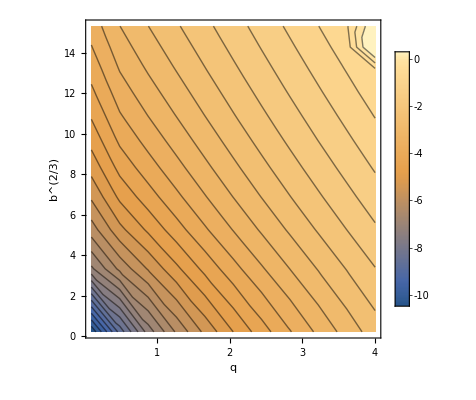

```mathematica
ListContourPlot[{#[[1]],#[[2]]^(2/3),Log[10,Abs[#[[3]]]]}&/@results1[[All,{1,2,3}]],FrameLabel->{"q","b^(2/3)","rel A"},PlotLegends->Automatic,PlotRange->All,Contours->30]
```

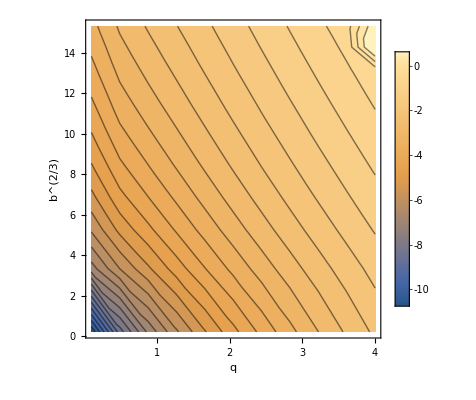

```mathematica
ListContourPlot[{#[[1]],#[[2]]^(2/3),Log[10,Abs[#[[3]]]]}&/@results1[[All,{1,2,4}]],FrameLabel->{"q","b^(2/3)","rel V"},PlotLegends->Automatic,PlotRange->All,Contours->30]
```

```mathematica
y/4+x==1
```

x+y/4==1

### Omega0 = 20

```mathematica
results2=Block[{s, Omega0,w, q,F,d,b,res,ra,rn,x,phi,par,s1},
Omega0=20;
d=1;
res={};
Do[
w=d*Omega0;
F=Sqrt[b/((1+q)*d^3)];

par={q,F,d};
s1=Sort[x/.Solve[Omega[x,0,0,par]==Omega0,x,Reals]];
rn={
4NIntegrate[
CylA[x,phi,Omega0,par],
{x,s1[[2]],s1[[3]]},
{phi,0,Pi/2}],
2NIntegrate[
CylR[x,phi,Omega0,par],
{x,s1[[2]],s1[[3]]},
{phi,0,Pi/2}]
};
ra=N[{d^2A[1/w,b,q],d^3V[1/w,b,q]}];

AppendTo[res,Join[{q,b},(ra-rn)/rn]],
{b,Subdivide[0.1,100,10]},{q,Subdivide[0.1,10,10]}];
res
];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

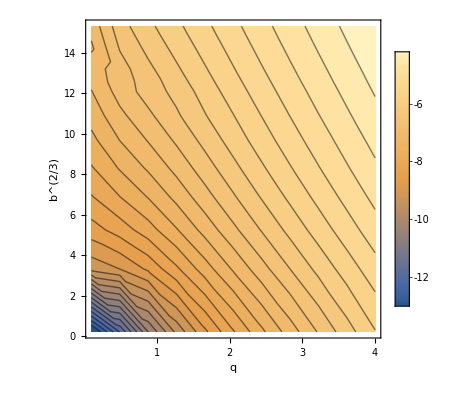

```mathematica
ListContourPlot[{#[[1]],#[[2]]^(2/3),Log[10,Abs[#[[3]]]]}&/@results2[[All,{1,2,3}]],FrameLabel->{"q","b^(2/3)","rel A"},PlotLegends->Automatic,PlotRange->All,Contours->30]
```

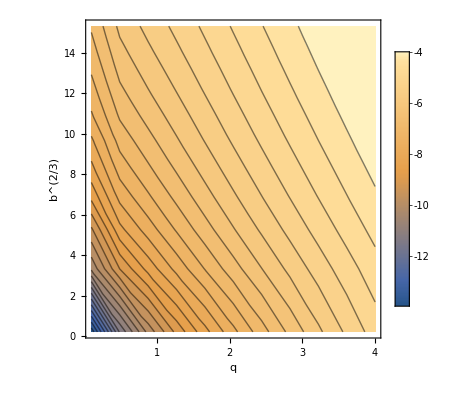

```mathematica
ListContourPlot[{#[[1]],#[[2]]^(2/3),Log[10,Abs[#[[3]]]]}&/@results2[[All,{1,2,4}]],FrameLabel->{"q","b^(2/3)","rel V"},PlotLegends->Automatic,PlotRange->All,Contours->30]
```

### Omega0 = 40

```mathematica
results3=Block[{s, Omega0,w, q,F,d,b,res,ra,rn,x,phi,par,s1},
Omega0=40;
d=1;
res={};
Do[
w=d*Omega0;
F=Sqrt[b/((1+q)*d^3)];

par={q,F,d};
s1=Sort[x/.Solve[Omega[x,0,0,par]==Omega0,x,Reals]];
rn={
4NIntegrate[
CylA[x,phi,Omega0,par],
{x,s1[[2]],s1[[3]]},
{phi,0,Pi/2}],
2NIntegrate[
CylR[x,phi,Omega0,par],
{x,s1[[2]],s1[[3]]},
{phi,0,Pi/2}]
};
ra=N[{d^2A[1/w,b,q],d^3V[1/w,b,q]}];

AppendTo[res,Join[{q,b},(ra-rn)/rn]],
{b,Subdivide[0.1,100,10]},{q,Subdivide[0.1,10,10]}];
res
];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

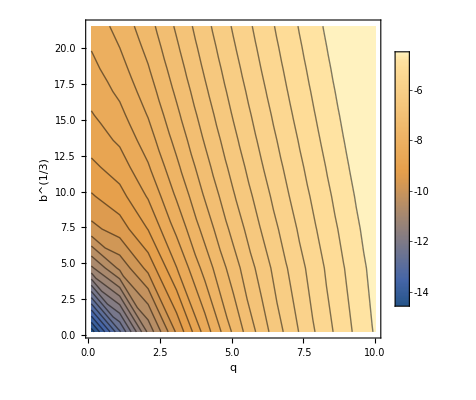

```mathematica
ListContourPlot[{#[[1]],#[[2]]^(2/3),Log[10,Abs[#[[3]]]]}&/@results3[[All,{1,2,3}]],FrameLabel->{"q","b^(1/3)","rel A"},PlotLegends->Automatic,PlotRange->All,Contours->30]
```

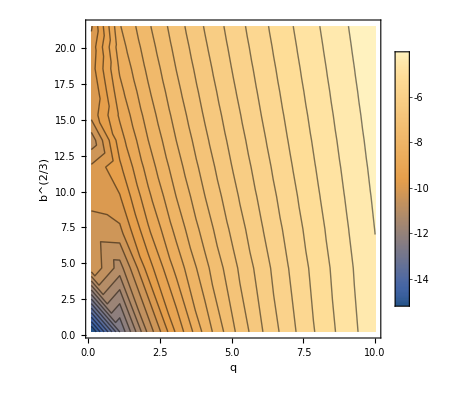

```mathematica
ListContourPlot[{#[[1]],#[[2]]^(2/3),Log[10,Abs[#[[3]]]]}&/@results3[[All,{1,2,4}]],FrameLabel->{"q","b^(2/3)","rel V"},PlotLegends->Automatic,PlotRange->All,Contours->30]
```

Concluding : 
In the limit of large w we find that the relative error in area integral grows as function of

	x = q + b^(2/3)/4 propto log(10,eps_A)
for fixed Omega,
We find that 
	x=1, Omega=10, log(10,epsA)=-7
	x=2, Omega=10, log(10,epsA)=-5 
	x=3, Omega=20, log(10,epsA)=-7
	x=6.5, Omega=40, log(10,epsA)=-7
	
Empirically we determine that  for relative precision eps_A < 10^-5 is 	

	w > 5.16*(q+b^(2/3)/4)  - 3.2

and

```mathematica
data={
{1,10,-7.14},
{2.1,10,-5},
{3.5,10,-3.14},
{2.1,20,-8.12},
{2.9,20,-7},
{6.3,40,-7.04},
{7.9,40,-6.08},
{4,40,-8.28}
};
f[x_,w_]=Fit[data,{1,x,w},{x,w}]
```

-5.61612-0.190029 w+0.981023 x

```mathematica
Table[f[d[[1]],d[[2]]],{d,data}]
```

{-6.53539,-5.45626,-4.08283,-7.35655,-6.57173,-7.03684,-5.4672,-9.29319}

```mathematica
Simplify[Solve[f[x,w]==-5.5,w]]
```

{{w→-0.611048+5.16249 x}}

### Extreme case

```mathematica
Block[{s, Omega, q,F,d,b},
Omega=30000;
d=1;
F=365;
q=3.00348934885*10^-6;
s=1/(d*Omega);
b=(1+q)F^2 d^3;
N[{d^2A[s,b,q],d^3V[1/Omega,b,q]}]
]
```

{1.39626×10^-8,1.5514×10^-13}

```mathematica
Block[{s, Omega, q,F,d,b},
Omega=30000;
d=1;
F=365;
q=3.00348934885*10^-6;
s=1/(d*Omega);
b=(1+q)F^2 d^3;
N[{d^2A[s,b,q],d^3V[1/Omega,b,q]}]
]
```

{1.39626×10^-8,1.5514×10^-13}

## Mathematica machine calculations

```mathematica
Omega[x_,y_,z_,{q_,F_,d_}]=FullSimplify[1/Sqrt[x^2+y^2+z^2]+q(1/Sqrt[x^2+y^2+z^2-2x d+d^2]-x/d^2)+1/2F^2(1+q)(x^2+y^2)]
```

-(q x)/d^2+1/2 F^2 (1+q) (x^2+y^2)+q/(√((d-x)^2+y^2+z^2))+1/(√(x^2+y^2+z^2))

### Overcontact case

```mathematica
par={0.5,0.5,1};
Omega0=2.65;
```

```mathematica
ContourPlot3D[Omega[x,y,z,par]==Omega0,{x,-1,2},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

```mathematica
region=ImplicitRegion[Omega[x,y,z,par]>=Omega0,{{x,-1,2},{y,-1,1},{z,-1,1}}]
```

ImplicitRegion[-0.5 x+0.1875 (x^2+y^2)+0.5/(√((1-x)^2+y^2+z^2))+1/(√(x^2+y^2+z^2))≥2.65&&-1≤x≤2&&-1≤y≤1&&-1≤z≤1,{x,y,z}]

```mathematica
RegionPlot3D[region,PlotPoints->60]
```

-Graphics3D-

```mathematica
Volume[region,Method->{"NIntegrate",WorkingPrecision->18}]
```

0.522778

```mathematica
disFine=DiscretizeRegion[region,AccuracyGoal->12,MaxCellMeasure->{"Area"->0.0005}]
```

MeshRegion[…]

```mathematica
Volume[disFine]
```

0.525653

```mathematica
Area[RegionBoundary[disFine]]
```

3.72616

### Generic case - left lobe

```mathematica
par={1,1,1};
Omega0=10;
```

```mathematica
ContourPlot3D[Omega[x,y,z,par]==Omega0,{x,-0.15,0.15},{y,-0.15,0.15},{z,-0.15,0.15},AxesLabel->{"x","y","z"}]
```

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics3D-

```mathematica
region=ImplicitRegion[Omega[x,y,z,par]>=Omega0,{{x,-0.15,0.15},{y,-0.15,0.15},{z,-0.15,0.15}}]
```

ImplicitRegion[-x+x^2+y^2+1/(√((1-x)^2+y^2+z^2))+1/(√(x^2+y^2+z^2))≥10&&-0.15≤x≤0.15&&-0.15≤y≤0.15&&-0.15≤z≤0.15,{x,y,z}]

```mathematica
RegionPlot3D[region,PlotPoints->200]
```

-Graphics3D-

```mathematica
Volume[region]
```

0.00576182

```mathematica
0.0057049894103252796
```

```mathematica
0.0057618175546174264
```

```mathematica
disFine=DiscretizeRegion[region,AccuracyGoal->12,MaxCellMeasure->{"Area"->10^-5}]
```

-Graphics3D-

```mathematica
Volume[disFine]
```

0.00572085

```mathematica
Area[RegionBoundary[disFine]]
```

0.154828

## Polishing zeros

1/2 ((2 q)/(√(R+(-1+t)^2))-2 q t+2/(√(R+t^2))+b (c R+t^2))== omega
 q/(√(R+(-1+t)^2))-q t+1/(√(R+t^2))+1/2 b (c R+t^2)==omega

```mathematica
D[q/(√(R+(-1+t)^2))-q t+1/(√(R+t^2))+1/2 b (c R+t^2),R]
```

(b c)/2-q/(2 (R+(-1+t)^2)^(3/2))-1/(2 (R+t^2)^(3/2))

## Equation for R at given t and c

Point is giben by:
	vec r = delta (t, R^(1/2)Cos[phi], R^(1/2)Sin[phi]}
where we introdue
	a=F^2 delta^3
	b=a(1+q)
	c=Cos[phi]^2

and rescaled refence potential
	omega=delta Omega0

1/2 ((2 q)/(√(R+(-1+t)^2))-2 q t+2/(√(R+t^2))+b (c R+t^2))== omega

 q/(√(R+(-1+t)^2))-q t+1/(√(R+t^2))+1/2 b (c R+t^2)==omega
 q/(√(R+(-1+t)^2))+1/(√(R+t^2))==omega-1/2 b (c R+t^2)+q t
 q^2/(R+(-1+t)^2)+1/(R+t^2)+(2q)/(√((R+(-1+t)^2)(R+t^2)))==(omega-1/2 b (c R+t^2)+q t)^2
(2q)/(√((R+(-1+t)^2)(R+t^2)))==(omega-1/2 b (c R+t^2)+q t)^2-q^2/(R+(-1+t)^2)-1/(R+t^2)
((omega-1/2 b (c R+t^2)+q t)^2-q^2/(R+(-1+t)^2)-1/(R+t^2))^2(R+(-1+t)^2)(R+t^2)-4q^2=0

```mathematica
TO1=Simplify[Together[((ω-1/2 b (c R+t^2)+q t)^2-q^2/(R+(-1+t)^2)-1/(R+t^2))^2(R+(-1+t)^2)(R+t^2)-4q^2]]
```

1/(16 (R+(-1+t)^2) (R+t^2))(16+b^4 c^4 R^8-64 t-4 b^3 (b+2 q) t^15+b^4 t^16-4 b t^13 (b^3+8 q^3+4 b^2 (3 q-2 ω)+12 b q (2 q-ω))+2 b^2 t^14 (3 b^2+16 b q+12 q^2-4 b ω)-32 t^2 (-3+q^2+ω^2)+64 t^3 (-1+q^2-q ω+2 ω^2)+2 b^3 c^3 R^7 (b (c-2 c t+2 t^2+2 c t^2)-4 (q t+ω))+b^2 c^2 R^6 (b^2 (6 t^4+8 c t^2 (1-2 t+2 t^2)+c^2 (1-4 t+10 t^2-12 t^3+6 t^4))-8 b (3 t^2+c (2-4 t+4 t^2)) (q t+ω)+24 (q t+ω)^2)+16 t^4 (1+q^4+2 b ω+16 q ω-12 ω^2+ω^4-2 q^2 (2+ω^2))+t^12 (b^4+16 q^4+16 b^3 (2 q-3 ω)+32 b q^2 (4 q-3 ω)+24 b^2 (6 q^2-8 q ω+ω^2))-8 t^11 (b^3 (q-4 ω)+8 q^3 (q-ω)+12 b q (2 q^2-4 q ω+ω^2)+12 b^2 (q^2-3 q ω+ω^2))-8 t^10 (b^3 ω+b^2 (1-2 q^2+24 q ω-18 ω^2)-4 q^2 (3 q^2-8 q ω+3 ω^2)+4 b (-4 q^3+18 q^2 ω-12 q ω^2+ω^3))+16 t^9 (b^2 (2+q^2+3 q ω-6 ω^2)-4 q (q^3-6 q^2 ω+6 q ω^2-ω^3)+2 b (q+12 q^2 ω-18 q ω^2+4 ω^3))-8 t^8 (b^2 (6+q^2-3 ω^2)+4 b (4 q+2 q^3-ω+2 q^2 ω-12 q ω^2+6 ω^3)+2 (q^4+16 q^3 ω+16 q ω^3-ω^4+q^2 (2-36 ω^2)))-8 t^6 (b^2-4 b (-4 q+6 ω+q^2 ω-ω^3)+4 (q^4-4 q^3 ω+ω^2-3 ω^4-2 q^2 (-3+ω^2)+8 q ω (-1+ω^2)))+32 t^5 (b (q-4 ω)+2 (-q^3 ω+q ω (-6+ω^2)-ω^2 (-2+ω^2)+q^2 (2+ω^2)))+32 t^7 (b^2+b (q^3-2 q^2 ω-3 q (-2+ω^2)+4 ω (-1+ω^2))+2 (q^4-ω^4+q^2 (2-6 ω^2)+q ω (-1+6 ω^2)))+2 b c R^5 (b^3 t^2 (2 t^4+c^3 (-1+t)^2 (1-2 t+2 t^2)+6 c t^2 (1-2 t+2 t^2)+2 c^2 (1-4 t+10 t^2-12 t^3+6 t^4))-4 b^2 (3 t^4+6 c t^2 (1-2 t+2 t^2)+c^2 (1-4 t+10 t^2-12 t^3+6 t^4)) (q t+ω)-16 (q t+ω)^3+4 b (6 t^2 (q t+ω)^2+c (-1+q^2 (-1+6 t^2-12 t^3+12 t^4)+12 q t (1-2 t+2 t^2) ω+6 (1-2 t+2 t^2) ω^2)))+R^4 (b^4 t^4 (c^4 (-1+t)^4+t^4+8 c^3 (-1+t)^2 (1-2 t+2 t^2)+8 c t^2 (1-2 t+2 t^2)+6 c^2 (1-4 t+10 t^2-12 t^3+6 t^4))-8 b^3 t^2 (t^4+2 c^3 (-1+t)^2 (1-2 t+2 t^2)+6 c t^2 (1-2 t+2 t^2)+3 c^2 (1-4 t+10 t^2-12 t^3+6 t^4)) (q t+ω)+16 (q t+ω)^4-32 b (q t+ω) (t^2 (q t+ω)^2+c (-1+q^2 (-1+2 t^2-4 t^3+4 t^4)+4 q t (1-2 t+2 t^2) ω+(2-4 t+4 t^2) ω^2))+8 b^2 (3 t^4 (q t+ω)^2+2 c t^2 (-1+q^2 (-1+6 t^2-12 t^3+12 t^4)+12 q t (1-2 t+2 t^2) ω+6 (1-2 t+2 t^2) ω^2)+c^2 (-2+q^2 (-1+2 t-12 t^3+30 t^4-36 t^5+18 t^6)+6 q t (1-4 t+10 t^2-12 t^3+6 t^4) ω+3 ω^2-36 t^3 ω^2+18 t^4 ω^2+t (4-12 ω^2)+t^2 (-3+30 ω^2))))+2 R^3 (b^4 t^6 (2 c^3 (-1+t)^4+6 c^2 (-1+t)^2 (1-2 t+2 t^2)+t^2 (1-2 t+2 t^2)+2 c (1-4 t+10 t^2-12 t^3+6 t^4))-4 b^3 t^4 (c^3 (-1+t)^4+6 c^2 (-1+t)^2 (1-2 t+2 t^2)+2 t^2 (1-2 t+2 t^2)+3 c (1-4 t+10 t^2-12 t^3+6 t^4)) (q t+ω)+16 (q t+ω)^2 (-1+q^2 (-1+t^2-2 t^3+2 t^4)+2 q t (1-2 t+2 t^2) ω+(1-2 t+2 t^2) ω^2)-16 b (q t+ω) (t^2 (-1+q^2 (-1+2 t^2-4 t^3+4 t^4)+4 q t (1-2 t+2 t^2) ω+(2-4 t+4 t^2) ω^2)+c (-2+q^2 (-1+2 t-2 t^2-4 t^3+10 t^4-12 t^5+6 t^6)+2 q t (1-4 t+10 t^2-12 t^3+6 t^4) ω+ω^2-12 t^3 ω^2+6 t^4 ω^2-4 t (-1+ω^2)+t^2 (-3+10 ω^2)))+4 b^2 (t^4 (-1+q^2 (-1+6 t^2-12 t^3+12 t^4)+12 q t (1-2 t+2 t^2) ω+6 (1-2 t+2 t^2) ω^2)+c^2 (-1+4 t+12 q^2 t^8+12 q t^7 (-3 q+2 ω)+4 t^3 (2+q^2+3 q ω-6 ω^2)-2 t^2 (4+q^2-3 ω^2)+6 t^6 (7 q^2-12 q ω+2 ω^2)-12 t^5 (2 q^2-7 q ω+3 ω^2)+3 t^4 (-1+q^2-16 q ω+14 ω^2))+2 c t^2 (-2+q^2 (-1+2 t-12 t^3+30 t^4-36 t^5+18 t^6)+6 q t (1-4 t+10 t^2-12 t^3+6 t^4) ω+3 ω^2-36 t^3 ω^2+18 t^4 ω^2+t (4-12 ω^2)+t^2 (-3+30 ω^2))))+2 R (16 q^4 (t^2-2 t^4+4 t^5-2 t^6-4 t^7+7 t^8-6 t^9+2 t^10)-16 q^3 t^3 (b t^2 (-2+4 t-t^2-8 t^3+14 t^4-12 t^5+4 t^6+c (-1+t)^2 (-1+t^2-2 t^3+t^4))+2 (2-4 t+t^2+8 t^3-14 t^4+12 t^5-4 t^6) ω)+4 q^2 (-4+8 t-12 b^2 (3+2 c) t^11+6 b^2 (2+c) t^12-24 b t^9 (b (1+c)-2 (3+c) ω)+6 b t^10 (b (7+6 c)-2 (4+c) ω)-2 t^6 (6+b^2 (1+c)+2 b (3+2 c) ω-84 ω^2)+4 t^7 (b^2 (1+c)+12 b (2+c) ω-36 ω^2)+16 t^3 (1+ω^2)-4 t^2 (3+2 ω^2)+4 t^4 (-8+b (2+c) ω+3 ω^2)-8 t^5 (-4+b (2+c) ω+12 ω^2)+t^8 (b^2 (3+4 c)-24 b (7+3 c) ω+48 ω^2))+(-1+t)^2 (-4+b^2 t^6-4 b t^4 ω+4 t^2 ω^2) (b^2 t^4 (1+2 c (-1+t)^2-2 t+2 t^2)-4 b t^2 (1+c (-1+t)^2-2 t+2 t^2) ω+4 (-1+(1-2 t+2 t^2) ω^2))-4 q (-1+t)^2 t (b^3 t^8 (2+3 c (-1+t)^2-4 t+4 t^2)-12 b^2 t^6 (1+c (-1+t)^2-2 t+2 t^2) ω-8 ω (-1+2 t-4 t^3 ω^2+4 t^4 ω^2+t^2 (-3+2 ω^2))+4 b t^2 (-1+2 t-12 t^3 ω^2+12 t^4 ω^2+t^2 (-3+6 ω^2)+c (-1+t)^2 (-1+3 t^2 ω^2))))+R^2 (16 q^4 (1-2 t^2+4 t^3-5 t^4-4 t^5+10 t^6-12 t^7+6 t^8)+b^4 t^8 (1+6 c^2 (-1+t)^4-4 t+10 t^2-12 t^3+6 t^4+8 c (-1+t)^2 (1-2 t+2 t^2))-8 b^3 t^6 (1+3 c^2 (-1+t)^4-4 t+10 t^2-12 t^3+6 t^4+6 c (-1+t)^2 (1-2 t+2 t^2)) ω-32 q^3 t (b t^2 (-1+2 t-2 t^2-4 t^3+10 t^4-12 t^5+6 t^6+c (-2+4 t-t^2-8 t^3+14 t^4-12 t^5+4 t^6))+2 (1-2 t+2 t^2+4 t^3-10 t^4+12 t^5-6 t^6) ω)+16 (1+(-4+8 t-6 t^2) ω^2+(1-4 t+10 t^2-12 t^3+6 t^4) ω^4)+8 q^2 (-12 b^2 (3+6 c+c^2) t^9+3 b^2 (6+8 c+c^2) t^10+8 t ω^2-12 b t^7 (b (1+4 c+c^2)-12 (1+c) ω)+6 b t^8 (b (5+14 c+3 c^2)-4 (3+2 c) ω)-t^4 (12+b^2 (1+4 c+c^2)+12 b c ω-120 ω^2)-4 (1+ω^2)+2 t^6 (b^2 c (3+c)-12 b (5+7 c) ω+36 ω^2)+4 t^2 (-2+b (ω+2 c ω))-8 t^3 (-2+6 ω^2+b (ω+2 c ω))+2 t^5 (b^2 (1+4 c+c^2)-72 ω^2+24 b (ω+2 c ω)))-32 b ω (c (-1+t)^2 (-1+2 t-4 t^3 ω^2+4 t^4 ω^2+t^2 (-3+2 ω^2))+t^2 (-2+ω^2-12 t^3 ω^2+6 t^4 ω^2-4 t (-1+ω^2)+t^2 (-3+10 ω^2)))+8 b^2 t^2 (c^2 (-1+t)^4 (-1+3 t^2 ω^2)+2 c (-1+t)^2 (-1+2 t-12 t^3 ω^2+12 t^4 ω^2+t^2 (-3+6 ω^2))+t^2 (-2+3 ω^2-36 t^3 ω^2+18 t^4 ω^2+t (4-12 ω^2)+t^2 (-3+30 ω^2)))-8 q t (b^3 t^6 (1+3 c^2 (-1+t)^4-4 t+10 t^2-12 t^3+6 t^4+6 c (-1+t)^2 (1-2 t+2 t^2))-6 b^2 t^4 (1+c^2 (-1+t)^4-4 t+10 t^2-12 t^3+6 t^4+4 c (-1+t)^2 (1-2 t+2 t^2)) ω-8 ω (-2+ω^2-12 t^3 ω^2+6 t^4 ω^2-4 t (-1+ω^2)+t^2 (-3+10 ω^2))+4 b (c (-1+t)^2 (-1+2 t-12 t^3 ω^2+12 t^4 ω^2+t^2 (-3+6 ω^2))+t^2 (-2+3 ω^2-36 t^3 ω^2+18 t^4 ω^2+t (4-12 ω^2)+t^2 (-3+30 ω^2))))))

```mathematica
Simplify[Series[Expand[Numerator[TO1]],{R,0,8}]]
```

(16-64 t-4 b^3 (b+2 q) t^15+b^4 t^16-4 b t^13 (b^3+8 q^3+4 b^2 (3 q-2 ω)+12 b q (2 q-ω))+2 b^2 t^14 (3 b^2+16 b q+12 q^2-4 b ω)-32 t^2 (-3+q^2+ω^2)+64 t^3 (-1+q^2-q ω+2 ω^2)+16 t^4 (1+q^4+2 b ω+16 q ω-12 ω^2+ω^4-2 q^2 (2+ω^2))+t^12 (b^4+16 q^4+16 b^3 (2 q-3 ω)+32 b q^2 (4 q-3 ω)+24 b^2 (6 q^2-8 q ω+ω^2))-8 t^11 (b^3 (q-4 ω)+8 q^3 (q-ω)+12 b q (2 q^2-4 q ω+ω^2)+12 b^2 (q^2-3 q ω+ω^2))-8 t^10 (b^3 ω+b^2 (1-2 q^2+24 q ω-18 ω^2)-4 q^2 (3 q^2-8 q ω+3 ω^2)+4 b (-4 q^3+18 q^2 ω-12 q ω^2+ω^3))+16 t^9 (b^2 (2+q^2+3 q ω-6 ω^2)-4 q (q^3-6 q^2 ω+6 q ω^2-ω^3)+2 b (q+12 q^2 ω-18 q ω^2+4 ω^3))-8 t^8 (b^2 (6+q^2-3 ω^2)+4 b (4 q+2 q^3-ω+2 q^2 ω-12 q ω^2+6 ω^3)+2 (q^4+16 q^3 ω+16 q ω^3-ω^4+q^2 (2-36 ω^2)))-8 t^6 (b^2-4 b (-4 q+6 ω+q^2 ω-ω^3)+4 (q^4-4 q^3 ω+ω^2-3 ω^4-2 q^2 (-3+ω^2)+8 q ω (-1+ω^2)))+32 t^5 (b (q-4 ω)+2 (-q^3 ω+q ω (-6+ω^2)-ω^2 (-2+ω^2)+q^2 (2+ω^2)))+32 t^7 (b^2+b (q^3-2 q^2 ω-3 q (-2+ω^2)+4 ω (-1+ω^2))+2 (q^4-ω^4+q^2 (2-6 ω^2)+q ω (-1+6 ω^2))))+2 (16 q^4 (t^2-2 t^4+4 t^5-2 t^6-4 t^7+7 t^8-6 t^9+2 t^10)-16 q^3 t^3 (b t^2 (-2+4 t-t^2-8 t^3+14 t^4-12 t^5+4 t^6+c (-1+t)^2 (-1+t^2-2 t^3+t^4))+2 (2-4 t+t^2+8 t^3-14 t^4+12 t^5-4 t^6) ω)+4 q^2 (-4+8 t-12 b^2 (3+2 c) t^11+6 b^2 (2+c) t^12-24 b t^9 (b (1+c)-2 (3+c) ω)+6 b t^10 (b (7+6 c)-2 (4+c) ω)-2 t^6 (6+b^2 (1+c)+2 b (3+2 c) ω-84 ω^2)+4 t^7 (b^2 (1+c)+12 b (2+c) ω-36 ω^2)+16 t^3 (1+ω^2)-4 t^2 (3+2 ω^2)+4 t^4 (-8+b (2+c) ω+3 ω^2)-8 t^5 (-4+b (2+c) ω+12 ω^2)+t^8 (b^2 (3+4 c)-24 b (7+3 c) ω+48 ω^2))+(-1+t)^2 (-4+b^2 t^6-4 b t^4 ω+4 t^2 ω^2) (b^2 t^4 (1+2 c (-1+t)^2-2 t+2 t^2)-4 b t^2 (1+c (-1+t)^2-2 t+2 t^2) ω+4 (-1+(1-2 t+2 t^2) ω^2))-4 q (-1+t)^2 t (b^3 t^8 (2+3 c (-1+t)^2-4 t+4 t^2)-12 b^2 t^6 (1+c (-1+t)^2-2 t+2 t^2) ω-8 ω (-1+2 t-4 t^3 ω^2+4 t^4 ω^2+t^2 (-3+2 ω^2))+4 b t^2 (-1+2 t-12 t^3 ω^2+12 t^4 ω^2+t^2 (-3+6 ω^2)+c (-1+t)^2 (-1+3 t^2 ω^2)))) R+(16 q^4 (1-2 t^2+4 t^3-5 t^4-4 t^5+10 t^6-12 t^7+6 t^8)+b^4 t^8 (1+6 c^2 (-1+t)^4-4 t+10 t^2-12 t^3+6 t^4+8 c (-1+t)^2 (1-2 t+2 t^2))-8 b^3 t^6 (1+3 c^2 (-1+t)^4-4 t+10 t^2-12 t^3+6 t^4+6 c (-1+t)^2 (1-2 t+2 t^2)) ω-32 q^3 t (b t^2 (-1+2 t-2 t^2-4 t^3+10 t^4-12 t^5+6 t^6+c (-2+4 t-t^2-8 t^3+14 t^4-12 t^5+4 t^6))+2 (1-2 t+2 t^2+4 t^3-10 t^4+12 t^5-6 t^6) ω)+16 (1+(-4+8 t-6 t^2) ω^2+(1-4 t+10 t^2-12 t^3+6 t^4) ω^4)+8 q^2 (-12 b^2 (3+6 c+c^2) t^9+3 b^2 (6+8 c+c^2) t^10+8 t ω^2-12 b t^7 (b (1+4 c+c^2)-12 (1+c) ω)+6 b t^8 (b (5+14 c+3 c^2)-4 (3+2 c) ω)-t^4 (12+b^2 (1+4 c+c^2)+12 b c ω-120 ω^2)-4 (1+ω^2)+2 t^6 (b^2 c (3+c)-12 b (5+7 c) ω+36 ω^2)+4 t^2 (-2+b (ω+2 c ω))-8 t^3 (-2+6 ω^2+b (ω+2 c ω))+2 t^5 (b^2 (1+4 c+c^2)-72 ω^2+24 b (ω+2 c ω)))-32 b ω (c (-1+t)^2 (-1+2 t-4 t^3 ω^2+4 t^4 ω^2+t^2 (-3+2 ω^2))+t^2 (-2+ω^2-12 t^3 ω^2+6 t^4 ω^2-4 t (-1+ω^2)+t^2 (-3+10 ω^2)))+8 b^2 t^2 (c^2 (-1+t)^4 (-1+3 t^2 ω^2)+2 c (-1+t)^2 (-1+2 t-12 t^3 ω^2+12 t^4 ω^2+t^2 (-3+6 ω^2))+t^2 (-2+3 ω^2-36 t^3 ω^2+18 t^4 ω^2+t (4-12 ω^2)+t^2 (-3+30 ω^2)))-8 q t (b^3 t^6 (1+3 c^2 (-1+t)^4-4 t+10 t^2-12 t^3+6 t^4+6 c (-1+t)^2 (1-2 t+2 t^2))-6 b^2 t^4 (1+c^2 (-1+t)^4-4 t+10 t^2-12 t^3+6 t^4+4 c (-1+t)^2 (1-2 t+2 t^2)) ω-8 ω (-2+ω^2-12 t^3 ω^2+6 t^4 ω^2-4 t (-1+ω^2)+t^2 (-3+10 ω^2))+4 b (c (-1+t)^2 (-1+2 t-12 t^3 ω^2+12 t^4 ω^2+t^2 (-3+6 ω^2))+t^2 (-2+3 ω^2-36 t^3 ω^2+18 t^4 ω^2+t (4-12 ω^2)+t^2 (-3+30 ω^2))))) R^2+2 (b^4 t^6 (2 c^3 (-1+t)^4+6 c^2 (-1+t)^2 (1-2 t+2 t^2)+t^2 (1-2 t+2 t^2)+2 c (1-4 t+10 t^2-12 t^3+6 t^4))-4 b^3 t^4 (c^3 (-1+t)^4+6 c^2 (-1+t)^2 (1-2 t+2 t^2)+2 t^2 (1-2 t+2 t^2)+3 c (1-4 t+10 t^2-12 t^3+6 t^4)) (q t+ω)+16 (q t+ω)^2 (-1+q^2 (-1+t^2-2 t^3+2 t^4)+2 q t (1-2 t+2 t^2) ω+(1-2 t+2 t^2) ω^2)-16 b (q t+ω) (t^2 (-1+q^2 (-1+2 t^2-4 t^3+4 t^4)+4 q t (1-2 t+2 t^2) ω+(2-4 t+4 t^2) ω^2)+c (-2+q^2 (-1+2 t-2 t^2-4 t^3+10 t^4-12 t^5+6 t^6)+2 q t (1-4 t+10 t^2-12 t^3+6 t^4) ω+ω^2-12 t^3 ω^2+6 t^4 ω^2-4 t (-1+ω^2)+t^2 (-3+10 ω^2)))+4 b^2 (t^4 (-1+q^2 (-1+6 t^2-12 t^3+12 t^4)+12 q t (1-2 t+2 t^2) ω+6 (1-2 t+2 t^2) ω^2)+c^2 (-1+4 t+12 q^2 t^8+12 q t^7 (-3 q+2 ω)+4 t^3 (2+q^2+3 q ω-6 ω^2)-2 t^2 (4+q^2-3 ω^2)+6 t^6 (7 q^2-12 q ω+2 ω^2)-12 t^5 (2 q^2-7 q ω+3 ω^2)+3 t^4 (-1+q^2-16 q ω+14 ω^2))+2 c t^2 (-2+q^2 (-1+2 t-12 t^3+30 t^4-36 t^5+18 t^6)+6 q t (1-4 t+10 t^2-12 t^3+6 t^4) ω+3 ω^2-36 t^3 ω^2+18 t^4 ω^2+t (4-12 ω^2)+t^2 (-3+30 ω^2)))) R^3+(b^4 t^4 (c^4 (-1+t)^4+t^4+8 c^3 (-1+t)^2 (1-2 t+2 t^2)+8 c t^2 (1-2 t+2 t^2)+6 c^2 (1-4 t+10 t^2-12 t^3+6 t^4))-8 b^3 t^2 (t^4+2 c^3 (-1+t)^2 (1-2 t+2 t^2)+6 c t^2 (1-2 t+2 t^2)+3 c^2 (1-4 t+10 t^2-12 t^3+6 t^4)) (q t+ω)+16 (q t+ω)^4-32 b (q t+ω) (t^2 (q t+ω)^2+c (-1+q^2 (-1+2 t^2-4 t^3+4 t^4)+4 q t (1-2 t+2 t^2) ω+(2-4 t+4 t^2) ω^2))+8 b^2 (3 t^4 (q t+ω)^2+2 c t^2 (-1+q^2 (-1+6 t^2-12 t^3+12 t^4)+12 q t (1-2 t+2 t^2) ω+6 (1-2 t+2 t^2) ω^2)+c^2 (-2+q^2 (-1+2 t-12 t^3+30 t^4-36 t^5+18 t^6)+6 q t (1-4 t+10 t^2-12 t^3+6 t^4) ω+3 ω^2-36 t^3 ω^2+18 t^4 ω^2+t (4-12 ω^2)+t^2 (-3+30 ω^2)))) R^4+2 b c (b^3 t^2 (2 t^4+c^3 (-1+t)^2 (1-2 t+2 t^2)+6 c t^2 (1-2 t+2 t^2)+2 c^2 (1-4 t+10 t^2-12 t^3+6 t^4))-4 b^2 (3 t^4+6 c t^2 (1-2 t+2 t^2)+c^2 (1-4 t+10 t^2-12 t^3+6 t^4)) (q t+ω)-16 (q t+ω)^3+4 b (6 t^2 (q t+ω)^2+c (-1+q^2 (-1+6 t^2-12 t^3+12 t^4)+12 q t (1-2 t+2 t^2) ω+6 (1-2 t+2 t^2) ω^2))) R^5+b^2 c^2 (b^2 (6 t^4+8 c t^2 (1-2 t+2 t^2)+c^2 (1-4 t+10 t^2-12 t^3+6 t^4))-8 b (3 t^2+c (2-4 t+4 t^2)) (q t+ω)+24 (q t+ω)^2) R^6+2 b^3 c^3 (b (c-2 c t+2 t^2+2 c t^2)-4 (q t+ω)) R^7+b^4 c^4 R^8+O[R]^9

```mathematica
coef1=Simplify[CoefficientList[num1,R]]
```

{16-64 t-4 b^3 (b+2 q) t^15+b^4 t^16-4 b t^13 (b^3+8 q^3+4 b^2 (3 q-2 γ)+12 b q (2 q-γ))+2 b^2 t^14 (3 b^2+16 b q+12 q^2-4 b γ)-32 t^2 (-3+q^2+γ^2)+64 t^3 (-1+q^2-q γ+2 γ^2)+16 t^4 (1+q^4+2 b γ+16 q γ-12 γ^2+γ^4-2 q^2 (2+γ^2))+t^12 (b^4+16 q^4+16 b^3 (2 q-3 γ)+32 b q^2 (4 q-3 γ)+24 b^2 (6 q^2-8 q γ+γ^2))-8 t^11 (b^3 (q-4 γ)+8 q^3 (q-γ)+12 b q (2 q^2-4 q γ+γ^2)+12 b^2 (q^2-3 q γ+γ^2))-8 t^10 (b^3 γ+b^2 (1-2 q^2+24 q γ-18 γ^2)-4 q^2 (3 q^2-8 q γ+3 γ^2)+4 b (-4 q^3+18 q^2 γ-12 q γ^2+γ^3))+16 t^9 (b^2 (2+q^2+3 q γ-6 γ^2)-4 q (q^3-6 q^2 γ+6 q γ^2-γ^3)+2 b (q+12 q^2 γ-18 q γ^2+4 γ^3))-8 t^8 (b^2 (6+q^2-3 γ^2)+4 b (4 q+2 q^3-γ+2 q^2 γ-12 q γ^2+6 γ^3)+2 (q^4+16 q^3 γ+16 q γ^3-γ^4+q^2 (2-36 γ^2)))-8 t^6 (b^2-4 b (-4 q+6 γ+q^2 γ-γ^3)+4 (q^4-4 q^3 γ+γ^2-3 γ^4-2 q^2 (-3+γ^2)+8 q γ (-1+γ^2)))+32 t^5 (b (q-4 γ)+2 (-q^3 γ+q γ (-6+γ^2)-γ^2 (-2+γ^2)+q^2 (2+γ^2)))+32 t^7 (b^2+b (q^3-2 q^2 γ-3 q (-2+γ^2)+4 γ (-1+γ^2))+2 (q^4-γ^4+q^2 (2-6 γ^2)+q γ (-1+6 γ^2))),2 (16 q^4 (t^2-2 t^4+4 t^5-2 t^6-4 t^7+7 t^8-6 t^9+2 t^10)-16 q^3 t^3 (b t^2 (-2+4 t-t^2-8 t^3+14 t^4-12 t^5+4 t^6+c (-1+t)^2 (-1+t^2-2 t^3+t^4))+2 (2-4 t+t^2+8 t^3-14 t^4+12 t^5-4 t^6) γ)+4 q^2 (-4+8 t-12 b^2 (3+2 c) t^11+6 b^2 (2+c) t^12-24 b t^9 (b (1+c)-2 (3+c) γ)+6 b t^10 (b (7+6 c)-2 (4+c) γ)-2 t^6 (6+b^2 (1+c)+2 b (3+2 c) γ-84 γ^2)+4 t^7 (b^2 (1+c)+12 b (2+c) γ-36 γ^2)+16 t^3 (1+γ^2)-4 t^2 (3+2 γ^2)+4 t^4 (-8+b (2+c) γ+3 γ^2)-8 t^5 (-4+b (2+c) γ+12 γ^2)+t^8 (b^2 (3+4 c)-24 b (7+3 c) γ+48 γ^2))+(-1+t)^2 (-4+b^2 t^6-4 b t^4 γ+4 t^2 γ^2) (b^2 t^4 (1+2 c (-1+t)^2-2 t+2 t^2)-4 b t^2 (1+c (-1+t)^2-2 t+2 t^2) γ+4 (-1+(1-2 t+2 t^2) γ^2))-4 q (-1+t)^2 t (b^3 t^8 (2+3 c (-1+t)^2-4 t+4 t^2)-12 b^2 t^6 (1+c (-1+t)^2-2 t+2 t^2) γ-8 γ (-1+2 t-4 t^3 γ^2+4 t^4 γ^2+t^2 (-3+2 γ^2))+4 b t^2 (-1+2 t-12 t^3 γ^2+12 t^4 γ^2+t^2 (-3+6 γ^2)+c (-1+t)^2 (-1+3 t^2 γ^2)))),16 q^4 (1-2 t^2+4 t^3-5 t^4-4 t^5+10 t^6-12 t^7+6 t^8)+b^4 t^8 (1+6 c^2 (-1+t)^4-4 t+10 t^2-12 t^3+6 t^4+8 c (-1+t)^2 (1-2 t+2 t^2))-8 b^3 t^6 (1+3 c^2 (-1+t)^4-4 t+10 t^2-12 t^3+6 t^4+6 c (-1+t)^2 (1-2 t+2 t^2)) γ-32 q^3 t (b t^2 (-1+2 t-2 t^2-4 t^3+10 t^4-12 t^5+6 t^6+c (-2+4 t-t^2-8 t^3+14 t^4-12 t^5+4 t^6))+2 (1-2 t+2 t^2+4 t^3-10 t^4+12 t^5-6 t^6) γ)+16 (1+(-4+8 t-6 t^2) γ^2+(1-4 t+10 t^2-12 t^3+6 t^4) γ^4)+8 q^2 (-12 b^2 (3+6 c+c^2) t^9+3 b^2 (6+8 c+c^2) t^10+8 t γ^2-12 b t^7 (b (1+4 c+c^2)-12 (1+c) γ)+6 b t^8 (b (5+14 c+3 c^2)-4 (3+2 c) γ)-t^4 (12+b^2 (1+4 c+c^2)+12 b c γ-120 γ^2)-4 (1+γ^2)+2 t^6 (b^2 c (3+c)-12 b (5+7 c) γ+36 γ^2)+4 t^2 (-2+b (γ+2 c γ))-8 t^3 (-2+6 γ^2+b (γ+2 c γ))+2 t^5 (b^2 (1+4 c+c^2)-72 γ^2+24 b (γ+2 c γ)))-32 b γ (c (-1+t)^2 (-1+2 t-4 t^3 γ^2+4 t^4 γ^2+t^2 (-3+2 γ^2))+t^2 (-2+γ^2-12 t^3 γ^2+6 t^4 γ^2-4 t (-1+γ^2)+t^2 (-3+10 γ^2)))+8 b^2 t^2 (c^2 (-1+t)^4 (-1+3 t^2 γ^2)+2 c (-1+t)^2 (-1+2 t-12 t^3 γ^2+12 t^4 γ^2+t^2 (-3+6 γ^2))+t^2 (-2+3 γ^2-36 t^3 γ^2+18 t^4 γ^2+t (4-12 γ^2)+t^2 (-3+30 γ^2)))-8 q t (b^3 t^6 (1+3 c^2 (-1+t)^4-4 t+10 t^2-12 t^3+6 t^4+6 c (-1+t)^2 (1-2 t+2 t^2))-6 b^2 t^4 (1+c^2 (-1+t)^4-4 t+10 t^2-12 t^3+6 t^4+4 c (-1+t)^2 (1-2 t+2 t^2)) γ-8 γ (-2+γ^2-12 t^3 γ^2+6 t^4 γ^2-4 t (-1+γ^2)+t^2 (-3+10 γ^2))+4 b (c (-1+t)^2 (-1+2 t-12 t^3 γ^2+12 t^4 γ^2+t^2 (-3+6 γ^2))+t^2 (-2+3 γ^2-36 t^3 γ^2+18 t^4 γ^2+t (4-12 γ^2)+t^2 (-3+30 γ^2)))),2 (b^4 t^6 (2 c^3 (-1+t)^4+6 c^2 (-1+t)^2 (1-2 t+2 t^2)+t^2 (1-2 t+2 t^2)+2 c (1-4 t+10 t^2-12 t^3+6 t^4))-4 b^3 t^4 (c^3 (-1+t)^4+6 c^2 (-1+t)^2 (1-2 t+2 t^2)+2 t^2 (1-2 t+2 t^2)+3 c (1-4 t+10 t^2-12 t^3+6 t^4)) (q t+γ)+16 (q t+γ)^2 (-1+q^2 (-1+t^2-2 t^3+2 t^4)+2 q t (1-2 t+2 t^2) γ+(1-2 t+2 t^2) γ^2)-16 b (q t+γ) (t^2 (-1+q^2 (-1+2 t^2-4 t^3+4 t^4)+4 q t (1-2 t+2 t^2) γ+(2-4 t+4 t^2) γ^2)+c (-2+q^2 (-1+2 t-2 t^2-4 t^3+10 t^4-12 t^5+6 t^6)+2 q t (1-4 t+10 t^2-12 t^3+6 t^4) γ+γ^2-12 t^3 γ^2+6 t^4 γ^2-4 t (-1+γ^2)+t^2 (-3+10 γ^2)))+4 b^2 (t^4 (-1+q^2 (-1+6 t^2-12 t^3+12 t^4)+12 q t (1-2 t+2 t^2) γ+6 (1-2 t+2 t^2) γ^2)+c^2 (-1+4 t+12 q^2 t^8+12 q t^7 (-3 q+2 γ)+4 t^3 (2+q^2+3 q γ-6 γ^2)-2 t^2 (4+q^2-3 γ^2)+6 t^6 (7 q^2-12 q γ+2 γ^2)-12 t^5 (2 q^2-7 q γ+3 γ^2)+3 t^4 (-1+q^2-16 q γ+14 γ^2))+2 c t^2 (-2+q^2 (-1+2 t-12 t^3+30 t^4-36 t^5+18 t^6)+6 q t (1-4 t+10 t^2-12 t^3+6 t^4) γ+3 γ^2-36 t^3 γ^2+18 t^4 γ^2+t (4-12 γ^2)+t^2 (-3+30 γ^2)))),b^4 t^4 (c^4 (-1+t)^4+t^4+8 c^3 (-1+t)^2 (1-2 t+2 t^2)+8 c t^2 (1-2 t+2 t^2)+6 c^2 (1-4 t+10 t^2-12 t^3+6 t^4))-8 b^3 t^2 (t^4+2 c^3 (-1+t)^2 (1-2 t+2 t^2)+6 c t^2 (1-2 t+2 t^2)+3 c^2 (1-4 t+10 t^2-12 t^3+6 t^4)) (q t+γ)+16 (q t+γ)^4-32 b (q t+γ) (t^2 (q t+γ)^2+c (-1+q^2 (-1+2 t^2-4 t^3+4 t^4)+4 q t (1-2 t+2 t^2) γ+(2-4 t+4 t^2) γ^2))+8 b^2 (3 t^4 (q t+γ)^2+2 c t^2 (-1+q^2 (-1+6 t^2-12 t^3+12 t^4)+12 q t (1-2 t+2 t^2) γ+6 (1-2 t+2 t^2) γ^2)+c^2 (-2+q^2 (-1+2 t-12 t^3+30 t^4-36 t^5+18 t^6)+6 q t (1-4 t+10 t^2-12 t^3+6 t^4) γ+3 γ^2-36 t^3 γ^2+18 t^4 γ^2+t (4-12 γ^2)+t^2 (-3+30 γ^2))),2 b c (b^3 t^2 (2 t^4+c^3 (-1+t)^2 (1-2 t+2 t^2)+6 c t^2 (1-2 t+2 t^2)+2 c^2 (1-4 t+10 t^2-12 t^3+6 t^4))-4 b^2 (3 t^4+6 c t^2 (1-2 t+2 t^2)+c^2 (1-4 t+10 t^2-12 t^3+6 t^4)) (q t+γ)-16 (q t+γ)^3+4 b (6 t^2 (q t+γ)^2+c (-1+q^2 (-1+6 t^2-12 t^3+12 t^4)+12 q t (1-2 t+2 t^2) γ+6 (1-2 t+2 t^2) γ^2))),b^2 c^2 (b^2 (6 t^4+8 c t^2 (1-2 t+2 t^2)+c^2 (1-4 t+10 t^2-12 t^3+6 t^4))-8 b (3 t^2+c (2-4 t+4 t^2)) (q t+γ)+24 (q t+γ)^2),2 b^3 c^3 (b (c-2 c t+2 t^2+2 c t^2)-4 (q t+γ)),b^4 c^4}

```mathematica
Length[coef1]
```

9

## Numerical stability of cross product -- seems flawless

### Case 1

```mathematica
Clear[ErrorCrossProduct1];
ErrorCrossProduct1[aa_,bb_,a_,b_]:=Module[{A,B},
A=N[{aa Cos[a],aa Sin[a],0}];
B=N[{bb Cos[b],bb Sin[b],0}];
Abs[Cross[A,B][[3]]]-aa bb Abs[Sin[a-b]]
]
```

```mathematica
n=100;
table1=Table[ErrorCrossProduct1[1,1,Pi*i/n,Pi*j/n],{i,0,n},{j,0,n}];
Mean[Flatten[Abs[table1]]]
```

5.28847×10^-17

```mathematica
ListPlot3D[table1,PlotRange->All]
```

-Graphics3D-

### Case 2

```mathematica
Clear[ErrorCrossProduct2];
ErrorCrossProduct2[aa_,bb_,a_,b_]:=Module[{A,B},
A=N[{aa(Cos[a]+1),aa Sin[a],0}];
B=N[{bb (Cos[b]+1),bb Sin[b],0}];
Abs[Cross[A,B][[3]]]-aa bb Abs[Sin[b]-Sin[a]+Sin[b-a]]
]
Expand[(1+Cos[a]) Sin[b]-(1+Cos[b]) Sin[a]]
```

-Sin[a]-Cos[b] Sin[a]+Sin[b]+Cos[a] Sin[b]

```mathematica
n=100;
table2=Table[ErrorCrossProduct2[2,1,Pi*i/n,Pi*j/n],{i,0,n},{j,0,n}];
Mean[Flatten[Abs[table2]]]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/4\ (1 - √5) + 1/4\ (-1 + √5).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/4\ (-1 - √5) + 1/4\ (1 + √5).

General::stop: Further output of N :: meprec will be suppressed during this calculation.

1.54883×10^-16

```mathematica
ListPlot3D[table2,PlotRange->All]
```

-Graphics3D-

```mathematica
FullSimplify[Cross[{Cos[a]+1,Sin[a],0},{Cos[b]+1,Sin[b],0}]]
```

{0,0,-(1+Cos[b]) Sin[a]+(1+Cos[a]) Sin[b]}